```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
Angulo1=Table[Drop[Import["Datos/Angulo1-"<>ToString[i]<>".dat","Data"],2,-1],{i,1,7}];
Angulo2=Table[Drop[Import["Datos/Angulo2-"<>ToString[i]<>".dat","Data"],2,-1],{i,1,10}];
Angulo3=Table[Drop[Import["Datos/Angulo3-"<>ToString[i]<>".dat","Data"],2,-1],{i,1,11}];
```

```mathematica
g=QuantityMagnitude[GeogravityModelData[{-33.04, -71.64, Quantity[108, "Meters"]}]["Magnitude"]]
```

9.79564

```mathematica
Clear[A,B,a,b,c,d,θ,μ,t,T,p]
A = a*(t)-b*(t)^2;
B = c -d*(t-T)^2;
T=t/.Solve[D[A,t]==0,t][[1]];
c=c/.Solve[{A/.t->T}=={B/.t->T},c][[1]]
b=g(Sin[θ]+Cos[θ]μ)/2;
d=g(Sin[θ]-Cos[θ]λ)/2;
F1[t_,angle_]:=Piecewise[{{A,t<T},{B,t>T}}]/.{θ->angle};
```

a^2/(4 b)

```mathematica
tD[dat_,t_]:= D[Normal[LinearModelFit[Table[dat[[i]],{i,t,t+2}],x,x]],x]
TDT[dat_]:= Table[{dat[[i,1]],tD[dat,i]},{i,1,Length[dat]-2}]
MaxT[dat_]:= dat[[Position[dat,Max[Drop[dat,0,1]]][[1,1]],1]]
fit1[dat_,θ_]:=NonlinearModelFit[dat,F1[t,θ],{{a,1},{λ,0.18},{μ,0.18}},t,MaxIterations->100000000000];
Plat[f_,dat_,x_,y_,label_]:=Plot[f,{t,0,dat[[-1,1]]},Epilog->{ PointSize[0.004],Red,Point[dat]},AxesLabel->{x,y},PlotLabel->label,PlotRange->{Min[Drop[dat,0,1]]*0.8,Max[Drop[dat,0,1]*1.2]}];
Plaat[f_,dat_,x_,y_,label_]:=Show[ListPlot[dat],Plot[f,{t,0,Max[dat[[All,All,1]]]*1.1}],AxesLabel->{x,y},PlotLabel->label];
Plit[f_,dat_,sty_]:= Plot[f,{t,0,dat[[-1,1]]},PlotRange->{Min[Drop[dat,0,1]],Max[Drop[dat,0,1]]},PlotStyle->{sty}]
```

```mathematica
x1=Table[fit1[Angulo1[[i]],14Degree],{i,1,7}];
VEL1 = Table[TDT[Angulo1[[i]]],{i,1,7}];
ACC1=Table[TDT[VEL1[[i]]],{i,1,7}];
μ1=Table[μ/.x1[[i]]["BestFitParameters"],{i,1,7}]
λ1=Table[λ/.x1[[i]]["BestFitParameters"],{i,1,7}]
```

{0.275966,0.231437,0.248404,0.262757,0.261091,0.273558,0.246876}

{0.197306,0.191439,0.192323,0.193908,0.195935,0.196018,0.190239}

```mathematica
x2=Table[fit1[Angulo2[[i]],21.5Degree],{i,1,10}];
VEL2= Table[TDT[Angulo2[[i]]],{i,1,10}];
ACC2=Table[TDT[VEL2[[i]]],{i,1,10}];
μ2=Table[μ/.x2[[i]]["BestFitParameters"],{i,1,10}]
λ2=Table[λ/.x2[[i]]["BestFitParameters"],{i,1,10}]
```

{0.176637,0.152192,0.147555,0.156397,0.157589,0.142063,0.154409,0.148083,0.161624,0.143223}

{0.260182,0.25456,0.250209,0.245424,0.25192,0.26046,0.248005,0.246667,0.240261,0.250207}

```mathematica
x3=Table[fit1[Angulo3[[i]],25.5Degree],{i,1,11}];
VEL3= Table[TDT[Angulo3[[i]]],{i,1,11}];
ACC3=Table[TDT[VEL3[[i]]],{i,1,11}];
μ3=Table[μ/.x3[[i]]["BestFitParameters"],{i,1,11}]
λ3=Table[λ/.x3[[i]]["BestFitParameters"],{i,1,11}]
```

{0.206951,0.215229,0.237955,0.235317,0.245151,0.255449,0.192598,0.22152,0.221255,0.181179,0.211061}

{0.205832,0.202665,0.197611,0.187928,0.183505,0.193602,0.224744,0.202036,0.201198,0.201269,0.197902}

```mathematica
Plot1=Table[Plat[Normal[x1[[i]]],Angulo1[[i]],"t[s]","x[m]","Mouse: posición vs tiempo "],{i,1,7}];
Plot2=Table[Plat[Normal[x2[[i]]],Angulo2[[i]],"t[s]","x[m]","Mouse: posición vs tiempo "],{i,1,10}];
Plot3=Table[Plat[Normal[x3[[i]]],Angulo3[[i]],"t[s]","x[m]","Mouse: posición vs tiempo "],{i,1,11}];
```

```mathematica
μ4=Join[μ1,μ2,μ3]
λ4=Join[λ1,λ2,λ3]
μ5=Join[μ4,λ4]
```

{0.275966,0.231437,0.248404,0.262757,0.261091,0.273558,0.246876,0.176637,0.152192,0.147555,0.156397,0.157589,0.142063,0.154409,0.148083,0.161624,0.143223,0.206951,0.215229,0.237955,0.235317,0.245151,0.255449,0.192598,0.22152,0.221255,0.181179,0.211061}

{0.197306,0.191439,0.192323,0.193908,0.195935,0.196018,0.190239,0.260182,0.25456,0.250209,0.245424,0.25192,0.26046,0.248005,0.246667,0.240261,0.250207,0.205832,0.202665,0.197611,0.187928,0.183505,0.193602,0.224744,0.202036,0.201198,0.201269,0.197902}

{0.275966,0.231437,0.248404,0.262757,0.261091,0.273558,0.246876,0.176637,0.152192,0.147555,0.156397,0.157589,0.142063,0.154409,0.148083,0.161624,0.143223,0.206951,0.215229,0.237955,0.235317,0.245151,0.255449,0.192598,0.22152,0.221255,0.181179,0.211061,0.197306,0.191439,0.192323,0.193908,0.195935,0.196018,0.190239,0.260182,0.25456,0.250209,0.245424,0.25192,0.26046,0.248005,0.246667,0.240261,0.250207,0.205832,0.202665,0.197611,0.187928,0.183505,0.193602,0.224744,0.202036,0.201198,0.201269,0.197902}

```mathematica
Plat1=Plaat[Normal[x1],Angulo1,"t[s]","x[m]","Mouse: posición vs tiempo, θ=14°"];
Plat2=Plaat[Normal[x2],Angulo2,"t[s]","x[m]","Mouse: posición vs tiempo , θ=21.5°"];
Plat3=Plaat[Normal[x3],Angulo3,"t[s]","x[m]","Mouse: posición vs tiempo , θ=25.5°"];
Export["Graf1.eps",Plat1]
Export["Graf2.eps",Plat2]
Export["Graf3.eps",Plat3]
```

Graf1.eps

Graf2.eps

Graf3.eps

```mathematica
Table[N[Round[{a,λ,μ}/.x1[[i]]["BestFitParameters"],10^Floor@Log[10,Abs[SetPrecision[x1[[1]]["ParameterErrors"],1]]]]],{i,1,7}]
```

{{1.36,0.1973,0.28},{1.21,0.1914,0.23},{1.3,0.1923,0.25},{1.51,0.1939,0.26},{1.47,0.1959,0.26},{1.48,0.196,0.27},{1.57,0.1902,0.25}}

```mathematica
Param1=Table[N[Round[{a,λ,μ}/.x1[[i]]["BestFitParameters"],10^Floor@Log[10,Abs[SetPrecision[x1[[i]]["ParameterErrors"],1]]]]],{i,1,7}];
Error1=Table[SetPrecision[x1[[i]]["ParameterErrors"],1],{i,1,7}];
ParamR1=Join[{{V0,λ,μ}},Table[Param1[[i,j]]±Error1[[i,j]],{i,1,7},{j,1,3}]]
```

{{V0,λ,μ},{1.36±0.02,0.1973±0.0006,0.28±0.02},{1.21±0.02,0.1914±0.0008,0.23±0.02},{1.3±0.02,0.1923±0.0007,0.25±0.02},{1.51±0.02,0.1939±0.0006,0.26±0.01},{1.47±0.02,0.1959±0.0006,0.26±0.02},{1.48±0.03,0.196±0.0006,0.27±0.02},{1.57±0.02,0.1902±0.0007,0.25±0.01}}

```mathematica
Param2=Table[N[Round[{a,λ,μ}/.x2[[i]]["BestFitParameters"],10^Floor@Log[10,Abs[SetPrecision[x2[[i]]["ParameterErrors"],1]]]]],{i,1,10}];
Error2=Table[SetPrecision[x2[[i]]["ParameterErrors"],1],{i,1,10}];
ParamR2=Join[{{V0,λ,μ}},Table[Param2[[i,j]]±Error2[[i,j]],{i,1,10},{j,1,3}]]
```

{{V0,λ,μ},{1.307±0.006,0.2602±0.0008,0.177±0.005},{1.235±0.008,0.2546±0.0008,0.152±0.007},{1.344±0.009,0.2502±0.0009,0.148±0.006},{1.426±0.009,0.2454±0.001,0.156±0.007},{1.254±0.009,0.2519±0.0009,0.158±0.007},{1.566±0.006,0.2605±0.0006,0.142±0.004},{1.575±0.008,0.248±0.0008,0.154±0.006},{1.254±0.009,0.2467±0.001,0.148±0.007},{1.3±0.01,0.24±0.001,0.162±0.008},{1.344±0.008,0.2502±0.0009,0.143±0.006}}

```mathematica
Param3=Table[N[Round[{a,λ,μ}/.x3[[i]]["BestFitParameters"],10^Floor@Log[10,Abs[SetPrecision[x3[[i]]["ParameterErrors"],1]]]]],{i,1,11}];
Error3=Table[SetPrecision[x3[[i]]["ParameterErrors"],1],{i,1,11}];
ParamR3=Join[{{V0,λ,μ}},Table[Param3[[i,j]]±Error3[[i,j]],{i,1,11},{j,1,3}]]
```

{{V0,λ,μ},{1.78±0.006,0.206±0.001,0.207±0.004},{1.774±0.009,0.203±0.002,0.215±0.006},{1.76±0.01,0.198±0.002,0.24±0.01},{1.8±0.01,0.188±0.002,0.235±0.01},{1.48±0.01,0.184±0.003,0.25±0.01},{1.69±0.02,0.194±0.003,0.26±0.01},{1.686±0.005,0.225±0.001,0.193±0.004},{1.64±0.01,0.202±0.002,0.222±0.008},{1.53±0.01,0.201±0.002,0.221±0.01},{1.43±0.01,0.201±0.002,0.181±0.009},{1.53±0.01,0.198±0.003,0.21±0.01}}

```mathematica
TableForm[ParamR1]
TableForm[ParamR2]
TableForm[ParamR3]
```

V0 | λ | μ
1.36±0.02 | 0.1973±0.0006 | 0.28±0.02
1.21±0.02 | 0.1914±0.0008 | 0.23±0.02
1.3±0.02 | 0.1923±0.0007 | 0.25±0.02
1.51±0.02 | 0.1939±0.0006 | 0.26±0.01
1.47±0.02 | 0.1959±0.0006 | 0.26±0.02
1.48±0.03 | 0.196±0.0006 | 0.27±0.02
1.57±0.02 | 0.1902±0.0007 | 0.25±0.01

V0 | λ | μ
1.307±0.006 | 0.2602±0.0008 | 0.177±0.005
1.235±0.008 | 0.2546±0.0008 | 0.152±0.007
1.344±0.009 | 0.2502±0.0009 | 0.148±0.006
1.426±0.009 | 0.2454±0.001 | 0.156±0.007
1.254±0.009 | 0.2519±0.0009 | 0.158±0.007
1.566±0.006 | 0.2605±0.0006 | 0.142±0.004
1.575±0.008 | 0.248±0.0008 | 0.154±0.006
1.254±0.009 | 0.2467±0.001 | 0.148±0.007
1.3±0.01 | 0.24±0.001 | 0.162±0.008
1.344±0.008 | 0.2502±0.0009 | 0.143±0.006

V0 | λ | μ
1.78±0.006 | 0.206±0.001 | 0.207±0.004
1.774±0.009 | 0.203±0.002 | 0.215±0.006
1.76±0.01 | 0.198±0.002 | 0.24±0.01
1.8±0.01 | 0.188±0.002 | 0.235±0.01
1.48±0.01 | 0.184±0.003 | 0.25±0.01
1.69±0.02 | 0.194±0.003 | 0.26±0.01
1.686±0.005 | 0.225±0.001 | 0.193±0.004
1.64±0.01 | 0.202±0.002 | 0.222±0.008
1.53±0.01 | 0.201±0.002 | 0.221±0.01
1.43±0.01 | 0.201±0.002 | 0.181±0.009
1.53±0.01 | 0.198±0.003 | 0.21±0.01

```mathematica
Error4=Join[Error1,Error2,Error3];
Mμ1=Mean[μ1];
Mμ2=Mean[μ2];
Mμ3=Mean[μ3];
Mμ4=Mean[μ3];
errμ1 =Max[SetPrecision[StandardDeviation[μ1],1],Sqrt[Sum[Error1[[All,3]][[i]]^2,{i,1,7}]]];
errμ2=Max[SetPrecision[StandardDeviation[μ2],1],Sqrt[Sum[Error2[[All,3]][[i]]^2,{i,1,10}]]];
errμ3 =Max[SetPrecision[StandardDeviation[μ3],1],Sqrt[Sum[Error3[[All,3]][[i]]^2,{i,1,11}]]];
errμ4 =Max[SetPrecision[StandardDeviation[μ4],1],Sqrt[Sum[Error4[[All,3]][[i]]^2,{i,1,7+10+11}]]];
Vμ1=N[Round[Mμ1,10^Floor@Log[10,Abs[errμ1]]]]±errμ1
Vμ2=N[Round[Mμ2,10^Floor@Log[10,Abs[errμ2]]]]±errμ2
Vμ3=N[Round[Mμ3,10^Floor@Log[10,Abs[errμ3]]]]±errμ3
Vμ4=N[Round[Mμ4,10^Floor@Log[10,Abs[errμ4]]]]±errμ4
```

0.26±0.04

0.15±0.02

0.22±0.03

0.22±0.06

```mathematica
Mλ1=Mean[λ1];
Mλ2=Mean[λ2];
Mλ3=Mean[λ3]
Mλ4=Mean[λ4];
errλ1 =Max[SetPrecision[StandardDeviation[λ1],1],Sqrt[Sum[Error1[[All,2]][[i]]^2,{i,1,7}]]];
errλ2=Max[SetPrecision[StandardDeviation[λ2],1],Sqrt[Sum[Error2[[All,2]][[i]]^2,{i,1,10}]]];
errλ3 =Max[SetPrecision[StandardDeviation[λ3],1],Sqrt[Sum[Error3[[All,2]][[i]]^2,{i,1,11}]]];
errλ4 =Max[SetPrecision[StandardDeviation[λ4],1],Sqrt[Sum[Error4[[All,2]][[i]]^2,{i,1,7+10+11}]]];
Vλ1=N[Round[Mλ1,10^Floor@Log[10,Abs[errλ1]]]]±errλ1
Vλ2=N[Round[Mλ2,10^Floor@Log[10,Abs[errλ2]]]]±errλ2
Vλ3=N[Round[Mλ3,10^Floor@Log[10,Abs[errλ3]]]]±errλ3
Vλ4=N[Round[Mλ4,10^Floor@Log[10,Abs[errλ4]]]]±errλ4
```

0.199845

0.194±0.003

0.251±0.006

0.2±0.01

0.22±0.03

```mathematica
Mμ5=Mean[μ5]
StandardDeviation[μ5]
Sqrt[Sum[Error4[[All,j]][[i]]^2,{i,1,7+10+11},{j,2,3}]]
Error4
errμ5 =Max[SetPrecision[StandardDeviation[μ5],1],Sqrt[Sum[Error4[[All,j]][[i]]^2,{i,1,7+10+11},{j,2,3}]]]
Vμ5=N[Round[Mμ5,10^Floor@Log[10,Abs[errμ5]]]]±errμ5
```

0.211194

0.0373172

0.06

{{0.02,0.0006,0.02},{0.02,0.0008,0.02},{0.02,0.0007,0.02},{0.02,0.0006,0.01},{0.02,0.0006,0.02},{0.03,0.0006,0.02},{0.02,0.0007,0.01},{0.006,0.0008,0.005},{0.008,0.0008,0.007},{0.009,0.0009,0.006},{0.009,0.001,0.007},{0.009,0.0009,0.007},{0.006,0.0006,0.004},{0.008,0.0008,0.006},{0.009,0.001,0.007},{0.01,0.001,0.008},{0.008,0.0009,0.006},{0.006,0.001,0.004},{0.009,0.002,0.006},{0.01,0.002,0.01},{0.01,0.002,0.01},{0.01,0.003,0.01},{0.02,0.003,0.01},{0.005,0.001,0.004},{0.01,0.002,0.008},{0.01,0.002,0.01},{0.01,0.002,0.009},{0.01,0.003,0.01}}

0.06

0.21±0.06

```mathematica
bar[{x_,y_},d_]:=Line[{{x,y-d/2},{x,y+d/2}}]
ldμ1=LearnDistribution[μ1,Method->"KernelDensityEstimation"]
ldμ2=LearnDistribution[μ2,Method->"KernelDensityEstimation"]
ldμ3=LearnDistribution[μ3,Method->"KernelDensityEstimation"]
ldμ4=LearnDistribution[μ4,Method->"KernelDensityEstimation"]
ldμ5=LearnDistribution[μ5,Method->"KernelDensityEstimation"]
ldλ1=LearnDistribution[λ1,Method->"KernelDensityEstimation"]
ldλ2=LearnDistribution[λ2,Method->"KernelDensityEstimation"]
ldλ3=LearnDistribution[λ3,Method->"KernelDensityEstimation"]
ldλ4=LearnDistribution[λ4,Method->"KernelDensityEstimation"]
```

LearnedDistribution[…]

LearnedDistribution[…]

LearnedDistribution[…]

«6 more identical outputs»

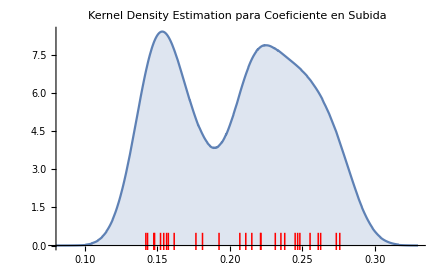

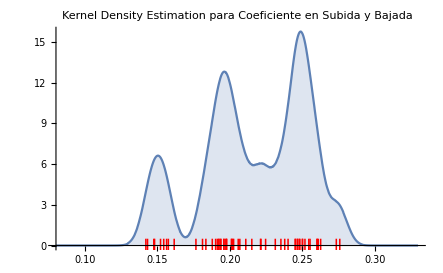

```mathematica
Show[Plot[PDF[ldμ1,x],{x,0.08,0.33},Filling->Bottom],NumberLinePlot[μ1,Spacings->0,PlotStyle->{Red,PointSize[0.01],Thickness[0.0025]}]/.{Point[{x_,y_}]:>bar[{x,y},0.05]},PlotLabel->"μ1"];
Show[Plot[PDF[ldμ2,x],{x,0.08,0.33},Filling->Bottom],NumberLinePlot[μ2,Spacings->0,PlotStyle->{Red,PointSize[0.01],Thickness[0.0025]}]/.{Point[{x_,y_}]:>bar[{x,y},0.05]},PlotLabel->"μ2"];

Show[Plot[PDF[ldμ3,x],{x,0.08,0.33},Filling->Bottom],NumberLinePlot[μ3,Spacings->0,PlotStyle->{Red,PointSize[0.01],Thickness[0.0025]}]/.{Point[{x_,y_}]:>bar[{x,y},0.05]},PlotLabel->"μ3"];

PMμ=Show[Plot[PDF[ldμ4,x],{x,0.08,0.33},Filling->Bottom],NumberLinePlot[μ4,Spacings->0,PlotStyle->{Red,PointSize[0.01],Thickness[0.0025]}]/.{Point[{x_,y_}]:>bar[{x,y},1]},PlotLabel->"Kernel Density Estimation para Coeficiente en Subida"]

PMμμ=Show[Plot[PDF[ldμ5,x],{x,0.08,0.33},Filling->Bottom],NumberLinePlot[μ5,Spacings->0,PlotStyle->{Red,PointSize[0.01],Thickness[0.0025]}]/.{Point[{x_,y_}]:>bar[{x,y},1]},PlotLabel->"Kernel Density Estimation para Coeficiente en Subida y Bajada"]
```

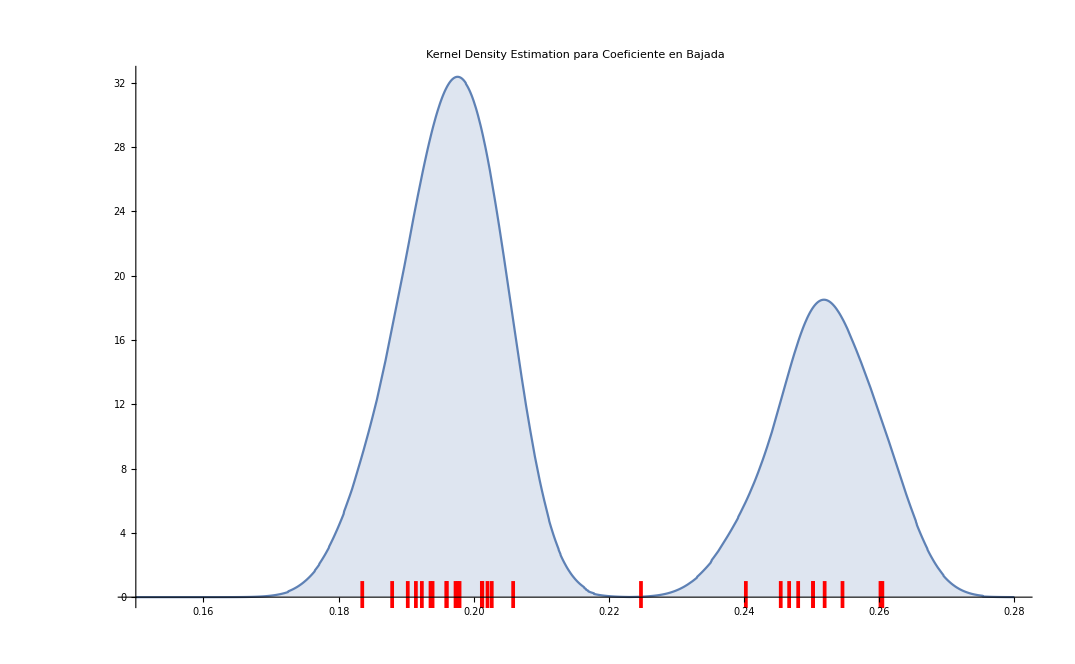

```mathematica
ldλ1=LearnDistribution[λ1,Method->"KernelDensityEstimation"];
Show[Plot[PDF[ldλ1,x],{x,0.185,0.205},Filling->Bottom],NumberLinePlot[λ1,Spacings->0,PlotStyle->{Red,PointSize[0.01],Thickness[0.0025]}]/.{Point[{x_,y_}]:>bar[{x,y},10]},PlotLabel->"λ1"];
Show[Plot[PDF[ldλ2,x],{x,0.23,0.28},Filling->Bottom],NumberLinePlot[λ2,Spacings->0,PlotStyle->{Red,PointSize[0.01],Thickness[0.0025]}]/.{Point[{x_,y_}]:>bar[{x,y},7]},PlotLabel->"λ2"];

Show[Plot[PDF[ldλ3,x],{x,0.15,0.25},Filling->Bottom],NumberLinePlot[λ3,Spacings->0,PlotStyle->{Red,PointSize[0.01],Thickness[0.0025]}]/.{Point[{x_,y_}]:>bar[{x,y},5]},PlotLabel->"λ3"];

PMλ=Show[Plot[PDF[ldλ4,x],{x,0.15,0.28},Filling->Bottom],NumberLinePlot[λ4,Spacings->0,PlotStyle->{Red,PointSize[0.01],Thickness[0.0025]}]/.{Point[{x_,y_}]:>bar[{x,y},2]},PlotLabel->"Kernel Density Estimation para Coeficiente en Bajada"]
```

```mathematica
Export["KDEsubida.eps",PMμ]
Export["KDEbajada.eps",PMλ]
Export["KDEsubidaBajada.eps",PMμμ]
```

KDEsubida.eps

KDEbajada.eps

KDEsubidaBajada.eps